```mathematica
V[x_,V0_]:=Piecewise[{{100000000,x<-1},{V0,-a<x<a},{100000000,1<x}}]/.a->1/4
tmp=ParametricNDSolve[{-ψ''[x]/2+V[x,V0]*ψ[x]==e*ψ[x],ψ[-1]==0,ψ'[-1]==1},ψ,{x,-1,1},{e,V0}]
```

{ψ→ParametricFunction[<>]}

ParametricNDSolve::prange: Invalid non-numeric value 0.75+0.5 n for parameter e.

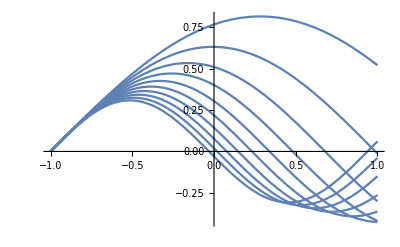

ParametricNDSolve::prange: Invalid non-numeric value 5+0.4 n for parameter e.

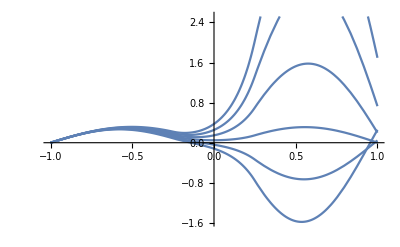

ParametricNDSolve::prange: Invalid non-numeric value -21.73+0.005 n for parameter e.

ParametricNDSolve::prange: Invalid non-numeric value -3+0.3 n for parameter e.

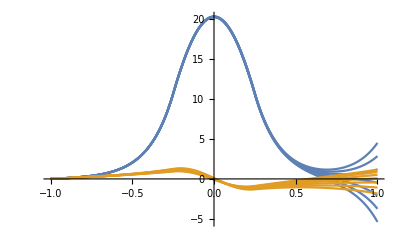

```mathematica
Plot[Table[Evaluate[ψ[.75+.5*n,0][t]/.tmp],{n,0,9}],{t,-1,1}]
Plot[Table[Evaluate[ψ[5+.4*n,30][t]/.tmp],{n,0,5}],{t,-1,1}]
Plot[{Table[Evaluate[ψ[-21.73+.005*n,-30][t]/.tmp],{n,0,6}],Table[Evaluate[ψ[-3+.3*n,-30][t]/.tmp],{n,0,6}]},{t,-1,1}]
```

InterpolatingFunction[…][x]

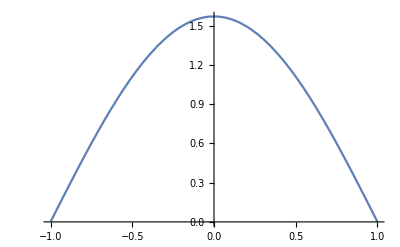

```mathematica
Psi[x_]=ψ[e/.FindRoot[ψ[e,0][1]/.tmp,{e,0}],0][x]/.tmp
Plot[Psi[x]/Integrate[Abs[Psi[y]]^2,{y,-1,1}],{x,-1,1}]
```

InterpolatingFunction[…][x]

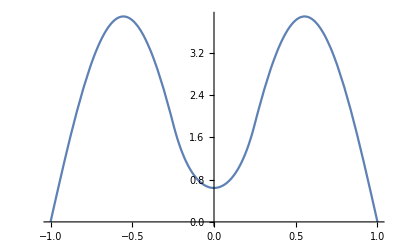

```mathematica
Psi[x_]=ψ[e/.FindRoot[ψ[e,30][1]/.tmp,{e,0}],30][x]/.tmp
Plot[Psi[x]/Integrate[Abs[Psi[y]]^2,{y,-1,1}],{x,-1,1}]
```

InterpolatingFunction[…][x]

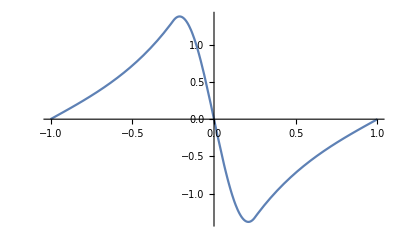

```mathematica
Psi[x_]=ψ[e/.FindRoot[ψ[e,-30][1]/.tmp,{e,0}],-30][x]/.tmp
Plot[Psi[x]/Integrate[Abs[Psi[y]]^2,{y,-1,1}],{x,-1,1}]
```